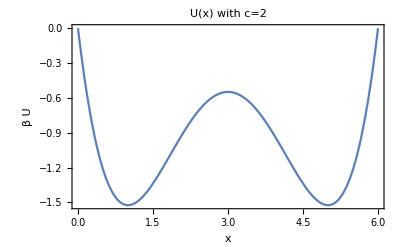

```mathematica
U1[x_,c_]:=Return[-x-3 c x-2 c^2 x+(3 x^2)/2+3 c x^2+c^2 x^2-x^3-c x^3+x^4/4];
U[r_,c_]:=(
x=Sqrt[r.r];
Return[U1[x,c]];
);
MyExp[x_]:=If[x<-40,0,Exp[x]];

Plot[U1[x,2]/4.1,{x,0,6},Frame->True,Axes->False,FrameLabel->{"x","β U"},PlotLabel->"U(x) with c=2"]
```

```mathematica
Metropolis[r_,rnew_,c_]:=(
e=U[r,c];
enew=U[rnew,c];
If[e>enew,
Return[True];
,
If[Random[]<MyExp[-(enew-e)/kT],
Return[True]
,
Return[False];
];
];
);
```

```mathematica
Distribution[data_,nbin_,minval_,maxval_]:=(bins=Table[{minval+i (maxval-minval)/nbin,0},{i,1,nbin}];
cnts=0;
Do[dat=data[[i]];(*pick a random value to bin*)Do[If[dat<bins[[j,1]],(*if that random value is smaller than the current bin,*)bins[[j,2]]+=1.;(*put it into the bin*)
cnts+=1;
Break[]; (*once we found its bin,stop!*)
];
,{j,1,nbin}];(*search over all bins*)
,{i,1,Length[data]}];(*check all numbers*)
Do[
bins[[i,1]]-=(maxval-minval)/nbin/2;(*shift the x axis to the center of the bins (for visualization purposes with few bins*)bins[[i,2]]*=nbin/(maxval-minval)/cnts;(*normalize the data*)
,{i,1,nbin}];
Return[bins];
);
```

```mathematica
RunUniformMC[dim_,nstep_,width_,c_]:=(
nreject=0;
r=Table[0,{i,1,dim}];
	rlist=Table[0,{i,1,nstep}];
Do[
rnew=r;
Do[
rnew[[i]]=width(2Random[]-1);
,{i,1,dim}];
If[Metropolis[r,rnew,2],
r=rnew;(*use metropolis to update*)
,
nreject+=1;(*if we don't update,store the rejection number*)
];
rlist[[step]]=Sqrt[r.r];(*add the location to the list,whether or not we changed it*)
,{step,1,nstep}]; (*iterate over nstep tries*)Print["Rejected ",100nreject/nstep//N,"% of trials"];


norm=NIntegrate[x^(dim-1)Exp[-U1[x,2]/kT],{x,0,∞}];
th=Plot[x^(dim-1)Exp[-U1[x,2]/kT]/norm,{x,.2,6.5},PlotRange->All];
sim=ListPlot[Distribution[rlist,50,.2,7]];
Show[sim,th,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"|r|","P(r)"},PlotLabel->"d = "<>ToString[dim]]
);
```

Rejected 39.825% of trials

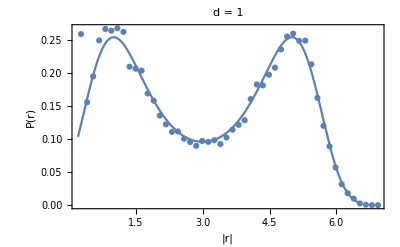

Rejected 62.97% of trials

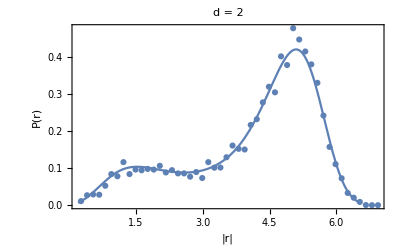

Rejected 81.405% of trials

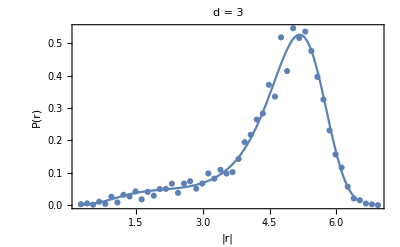

Rejected 98.755% of trials

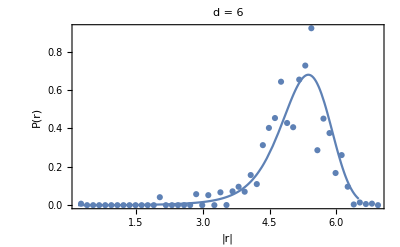

```mathematica
RunUniformMC[1,20000,8,2]
RunUniformMC[2,20000,8,2]
RunUniformMC[3,20000,8,2]
RunUniformMC[6,20000,8,2]
```